## Branch cut region in Xi-space

```mathematica
dz=0.001;
IsEndangered[x_]:=AnyTrue[IterChain[x],
Abs[#]<0.01∨Im[#]<lbp+dz ∨Im[#]>lbp+2π-dz&];

IsConsistentX[x_]:=Abs[XiInv[Xi[x]]-x]<0.001;
IsConsistentXi[xi_]:=Abs[Xi[XiInv[xi]]-xi]<0.001;
IsExping[x_]:=Abs[FracExp[x,1]-Exp[x]]<0.001;

IsHalfExping[x_]:=Abs[FracExp[FracExp[x,1/2],1/2]-Exp[x]]<0.001;
IsLogExping[x_,n_]:=Abs[FracExp[FracExp[x,n],-n]-x]<0.001;
```

```mathematica
MaxSafeCPStep[xi_,MaxStep_,DStep_]:=
SelectFirst[
Table[{n,IsEndangered[XiInv[xi CP^n]]},{n,0,MaxStep,DStep}],
#⟦2⟧==True&,{MaxStep}]⟦1⟧;
MaxSafeFracIterations[x_,MaxStep_:1,DStep_:0.05]:=MaxSafeCPStep[Xi[x],MaxStep,DStep];
```

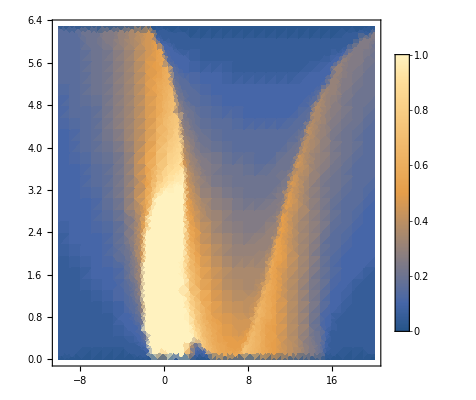

```mathematica
DensityPlot[MaxSafeFracIterations[x+I y],{x,xmin,xmax},{y,ymin,ymax},
PlotPoints->30,PlotLegends->Automatic]
```

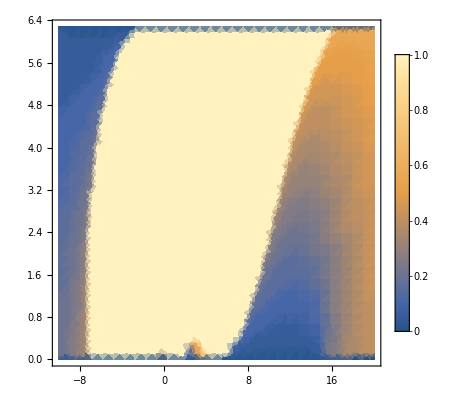

```mathematica
DensityPlot[-MaxSafeFracIterations[x+I y,-1,-0.05],{x,xmin,xmax},{y,ymin,ymax},
PlotPoints->30,PlotLegends->Automatic]
```

```mathematica
MaxConsistentCPStep[xi_,StartStep_,EndStep_,DStep_]:=
SelectFirst[
Table[{n,IsConsistentXi[xi CP^n]},{n,StartStep,EndStep,DStep}],
#⟦2⟧==False&,{EndStep}]⟦1⟧;
MaxConsistentFracIterations[x_,StartStep_:0,MaxStep_:1,DStep_:0.05]:=
MaxConsistentCPStep[Xi[x],StartStep,MaxStep,DStep];
```

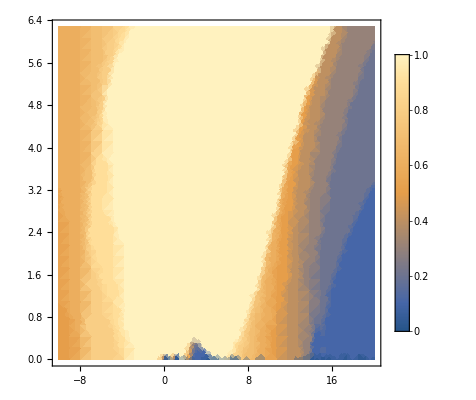

```mathematica
DensityPlot[MaxConsistentFracIterations[x+I y,0,1,0.1],{x,xmin,xmax},{y,ymin,ymax},
PlotPoints->30,PlotLegends->Automatic]
```

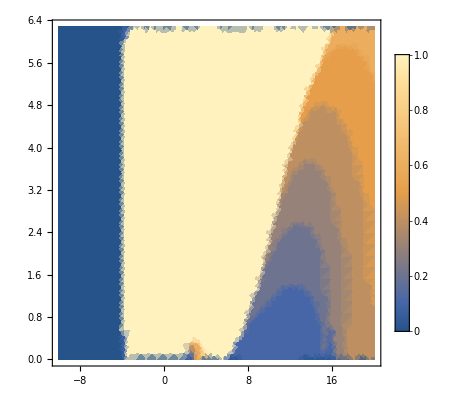

```mathematica
DensityPlot[1-MaxConsistentFracIterations[x+I y,1,0,-0.1],{x,xmin,xmax},{y,ymin,ymax},
PlotPoints->30,PlotLegends->Automatic]
```

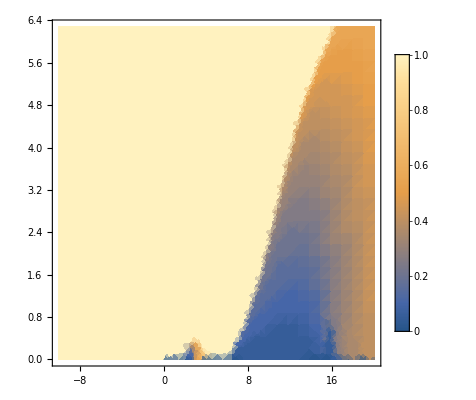

```mathematica
DensityPlot[-MaxConsistentFracIterations[x+I y,-1,-0.05],{x,xmin,xmax},{y,ymin,ymax},
PlotPoints->30,PlotLegends->Automatic]
```

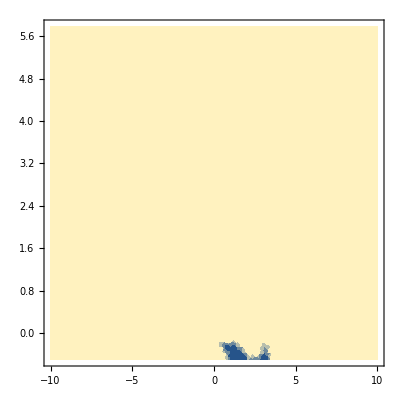

```mathematica
lbp=-0.5;
xmin=-10;xmax=10;
(*ymin=lbp-1;ymax=lbp+2π+1;*)
ymin=lbp;ymax=lbp+2π;
DensityPlot[If[IsLogExping[x+I y,-0.1],1,0],{x,xmin,xmax},{y,ymin,ymax},
PlotPoints->30]
```

```mathematica
IsLogExping[0.1,-1]
```

True

```mathematica
v=Exp[1]+0.03;
RequiredIters[v]
MinIterVal[v]
MaxIterVal[v]
IsEndangered[v]
IsExping[0.1]
```

35

0.0109161

3.91202

True

True

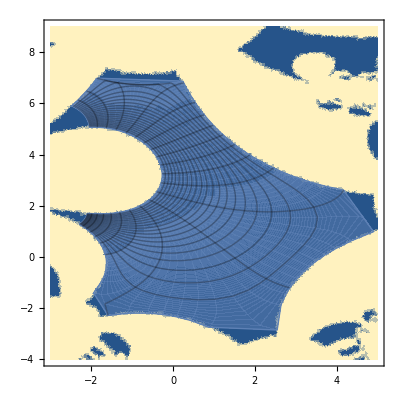

```mathematica
lbp=-0;
xmin=-10;xmax=20;
ymin=lbp;ymax=lbp+2π;
ximin=-3;ximax=5;
yimin=-4;yimax=9;
Show[
DensityPlot[If[IsEndangered[XiInv[x+I y]],10,0],{x,ximin,ximax},{y,yimin,yimax},
PlotPoints->60],
ParametricPlot[Xi[x+I y]//CPnt,{x,xmin,xmax},{y,ymin,ymax},
Mesh->20,PlotRange->Full,PlotStyle->Opacity[0.5],PlotPoints->50]
]
```

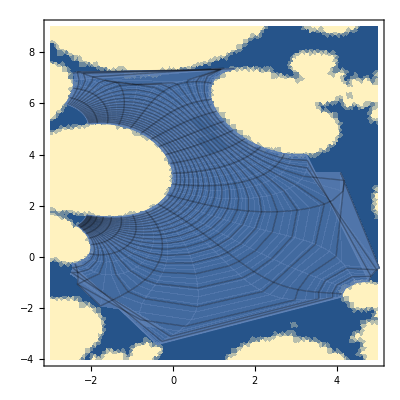
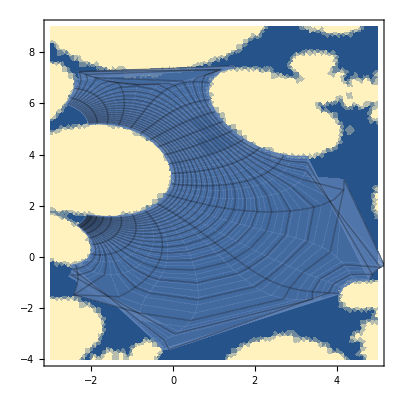
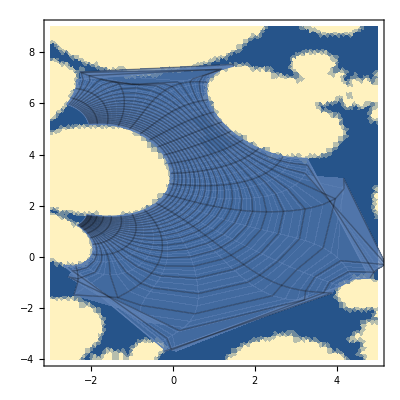
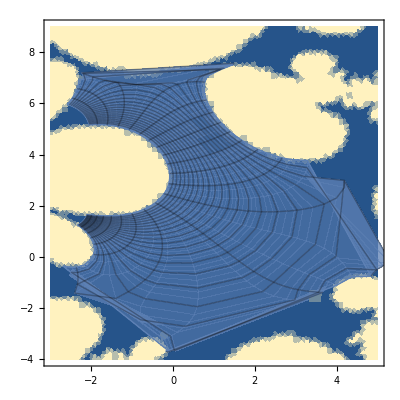
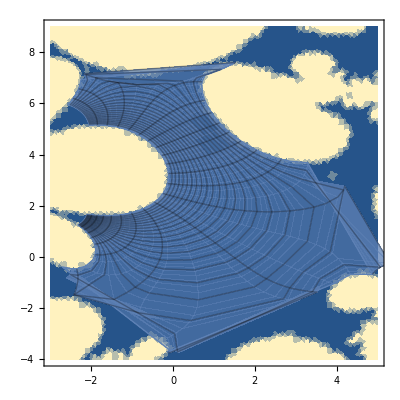
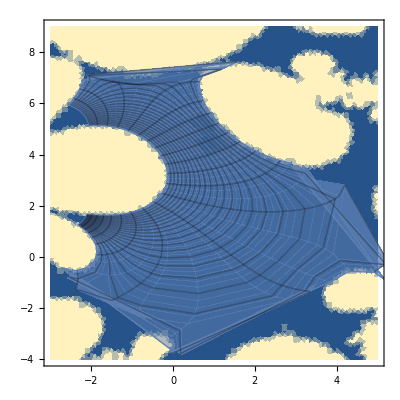
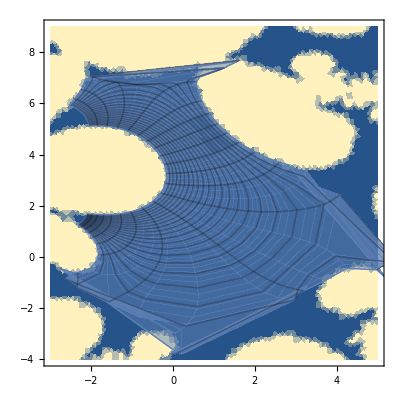
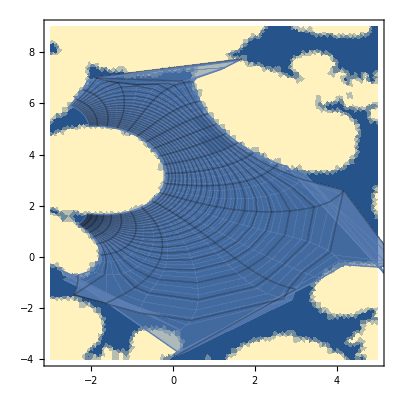

```mathematica
Table[lbp=bp;ymin=lbp;ymax=lbp+2π;
Show[
DensityPlot[If[IsEndangered[XiInv[x+I y]],10,0],{x,ximin,ximax},{y,yimin,yimax},PlotPoints->30],
ParametricPlot[Xi[x+I y]//CPnt,{x,xmin,xmax},{y,ymin,ymax},
Mesh->20,PlotRange->Full,PlotStyle->Opacity[0.5]]
],
{bp,-1,0,0.1}]
```

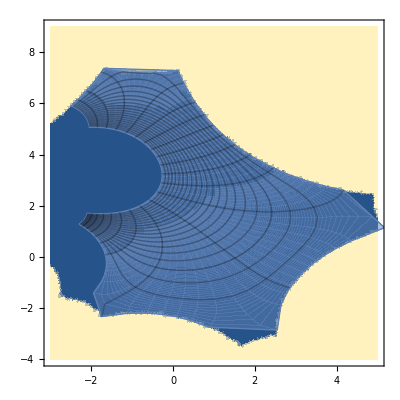

```mathematica
Show[
DensityPlot[If[IsConsistentXi[x+I y],0,1],{x,ximin,ximax},{y,yimin,yimax},
PlotPoints->60],
ParametricPlot[Xi[x+I y]//CPnt,{x,xmin,xmax},{y,ymin,ymax},
Mesh->20,PlotRange->Full,PlotStyle->Opacity[0.5],PlotPoints->50]
]
```

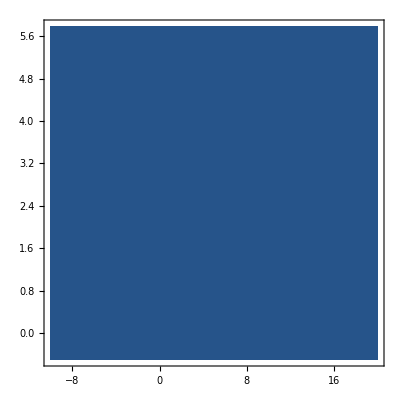

```mathematica
DensityPlot[If[IsConsistentX[x+I y],0,1],{x,xmin,xmax},{y,ymin,ymax},
PlotPoints->50]
```

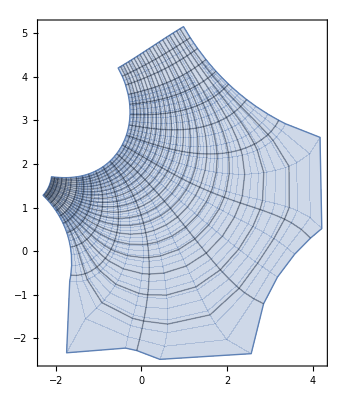

```mathematica
lbp=0;
xmin=-10;xmax=10;
ymin=lbp;ymax=lbp+2π;
ParametricPlot[Xi[x+I y]//CPnt,{x,xmin,xmax},{y,ymin,ymax},
Mesh->20,PlotRange->Full]
```

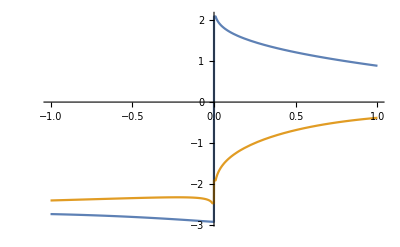

```mathematica
Plot[{Re[Xi[1+y I]],Re[Xi[0+y I]]},{y,-1,1}]
```

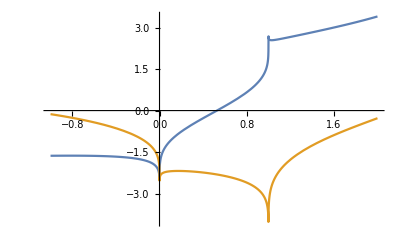

```mathematica
lbp=0;
Plot[{Re[Xi[x]],Im[Xi[x]]},{x,-1,2}]
```

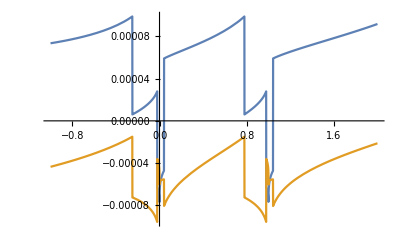

```mathematica
Plot[{Re[InnerTarget[x]],Im[InnerTarget[x]]},{x,-1,2}]
```

```mathematica
InnerTarget[2.3]
```

0.318142+1.33716 ⅈ

```mathematica
lbp=0;
Manipulate[
GraphicsGrid[{{
Plot[{Re[Xi[x+y I]],Im[Xi[x+y I]]},{x,-1,2}],
Plot[{Re[InnerTarget[x+y I]],Im[InnerTarget[x+y I]]},{x,-1,2}]
},{
,Plot[RequiredIters[x+y I],{x,-1,2}]
}}],{y,0,0.2}]
```

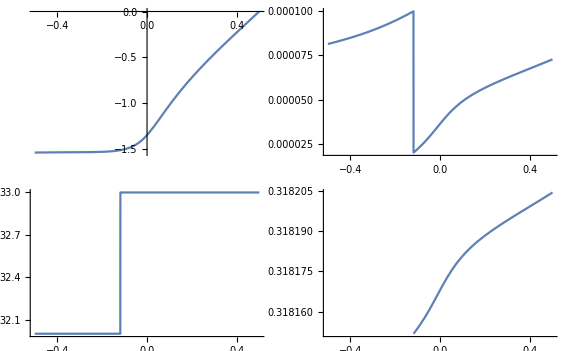

```mathematica
lbp=0;y=0.1;
xmin=-0.5;xmax=0.5;
GraphicsGrid[{{
Plot[{Re[Xi[x+y I]](*,Im[Xi[x+y I]]*)},{x,xmin,xmax}],
Plot[{Re[InnerTarget[x+y I]](*,Im[InnerTarget[x+y I]]*)},{x,xmin,xmax}]
},{
Plot[RequiredIters[x+y I]+1,{x,xmin,xmax}],
Plot[Re[IterChain[x+y I]⟦33⟧],{x,xmin,xmax}]//Quiet
}}]
```

```mathematica
XiForce[x_,iters_]:=
CP^iters (RepFunc[LogB,iters][x]-CP);
```

```mathematica
XiForce[3,1]
```

2.03649+0.61827 ⅈ

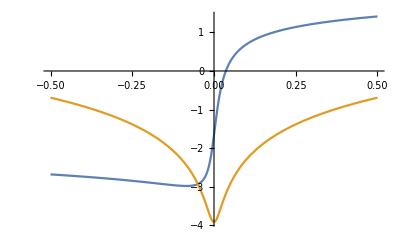

```mathematica
y=0.02;
Plot[{Re[XiForce[x+y I,1]],Re[LogB[x+y I]]},{x,xmin,xmax}]
```

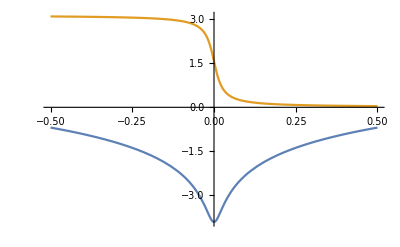

```mathematica
y=0.02;
Plot[{Re[Log[x+y I]],Im[Log[x+y I]]},{x,xmin,xmax}]
```

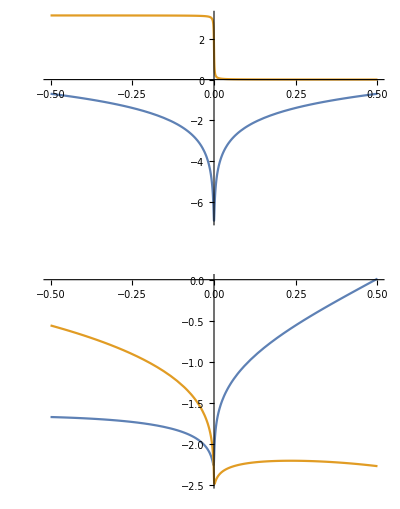

```mathematica
y=0.001;n=10;
GraphicsColumn[{
Plot[{Re[LogB[x+y I]],Im[LogB[x+y I]]},{x,xmin,xmax}],
Plot[{Re[XiForce[x+y I,n]],Im[XiForce[x+y I,n]]},{x,xmin,xmax}]
}]
```

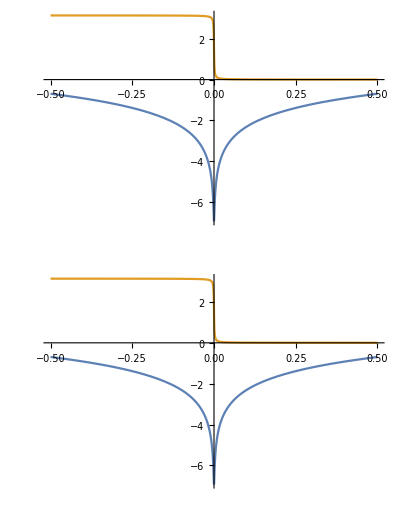

```mathematica
y=0.001;
GraphicsColumn[{
Plot[{Re[Log[x+y I]],Im[Log[x+y I]]},{x,xmin,xmax}],
Plot[{Re[LogB[x+y I]],Im[LogB[x+y I]]},{x,xmin,xmax}]
}]
```

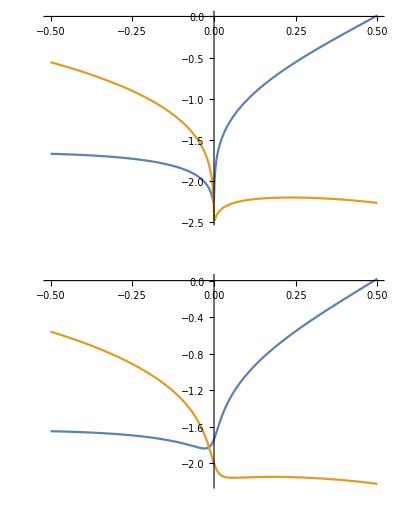

```mathematica
y=0.001;n=10;
GraphicsColumn[{
Plot[{Re[XiForce[x+0.001 I,n]],Im[XiForce[x+0.001 I,n]]},{x,xmin,xmax}],
Plot[{Re[XiForce[x+0.02I,n]],Im[XiForce[x+0.02I,n]]},{x,xmin,xmax}]
}]
```

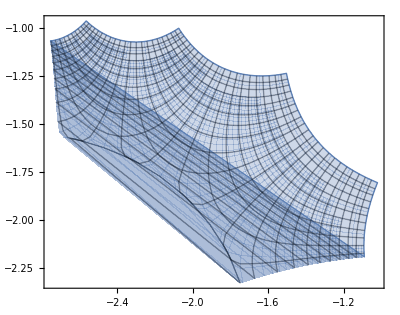

```mathematica
lbp=0;
xmin=-0.1;xmax=0.1;
ymin=-0.1;ymax=0.1;
ParametricPlot[Xi[x+I y]//CPnt,{x,xmin,xmax},{y,ymin,ymax},
Mesh->20,PlotRange->Full]
```

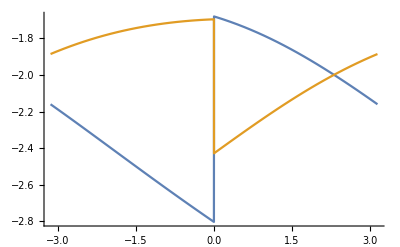

```mathematica
r=0.01;n=10; lbp=0;
GraphicsColumn[{
Plot[{Re[XiForce[r Exp[I ϕ],n]],Im[XiForce[r Exp[I ϕ],n]]},{ϕ,-π,π}]
}]
```